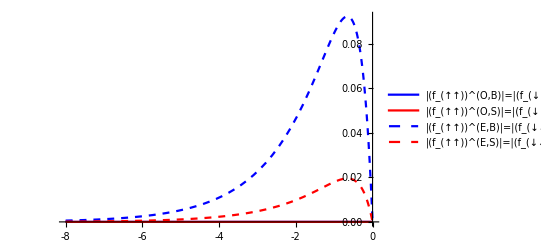

```mathematica
J=3;
S=1/2;
m1=-1/2;
n1=-3/2;
F2=Sqrt[(S-m1)*(S+m1+1)];
F4=Sqrt[(S-n1)*(S+n1+1)];
Δ=√2;
μ=-1;
n=0.000001;
η=1;
ξ=2/Δ;
ϕ=Pi/5;
EE1=Δ*(μ-Δ^2/4)^(1/2);
EE2=Abs[μ];
kI1=I*((Δ^2/2-μ)+(n^2-EE1^2)^(1/2))^(1/2);
kI2=-I*((Δ^2/2-μ)-(n^2-EE1^2)^(1/2))^(1/2);
kC1=((μ-Δ^2/2)+I*(EE1^2-n^2)^(1/2))^(1/2);
kC2=((μ-Δ^2/2)-I*(EE1^2-n^2)^(1/2))^(1/2);
qe=kI1;
qh=kI2;
γe=(n+qe^2-μ)/(Δ*qe);
γh=(n+qh^2-μ)/(Δ*qh);
γγe=-γe;
γγh=-γh;
Clear[α11,α12,α13,α14,α21,α22,α23,α24,α31,α32,α33,α34,α41,α42,α43,α44,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44];
x1=0;
G[ϕ_]:=({{-γe/((1+Abs[γe]^2)^(1/2)), 0, γh/((1+Abs[γh]^2)^(1/2)), 0, -γe*Exp[I*ϕ]/((1+Abs[γe]^2)^(1/2)), 0, γh/((1+Abs[γh]^2)^(1/2))*Exp[I*ϕ], 0}, {0, -γe/((1+Abs[γe]^2)^(1/2)), 0, γh/((1+Abs[γh]^2)^(1/2)), 0, -γe/((1+Abs[γe]^2)^(1/2))*Exp[I*ϕ], 0, γh/((1+Abs[γh]^2)^(1/2))*Exp[I*ϕ]}, {1/((1+Abs[γe]^2)^(1/2)), 0, 1/((1+Abs[γh]^2)^(1/2)), 0, -1/((1+Abs[γe]^2)^(1/2)), 0, -1/((1+Abs[γh]^2)^(1/2)), 0}, {0, 1/((1+Abs[γe]^2)^(1/2)), 0, 1/((1+Abs[γh]^2)^(1/2)), 0, -1/((1+Abs[γe]^2)^(1/2)), 0, -1/((1+Abs[γh]^2)^(1/2))}, {(-2*I*qe*γe-I*Δ+I*Δ*Exp[I*ϕ]-J*m1*γe)/((1+Abs[γe]^2)^(1/2)), J*F2*-γe/((1+Abs[γe]^2)^(1/2)), (-2*I*qh*γh-I*Δ+I*Δ*Exp[I*ϕ]+J*m1*γh)/((1+Abs[γh]^2)^(1/2)), J*F2*γh/((1+Abs[γh]^2)^(1/2)), 2*I*qe*γe/((1+Abs[γe]^2)^(1/2))*Exp[I*ϕ], 0, 2*I*qh*γh/((1+Abs[γh]^2)^(1/2))*Exp[I*ϕ], 0}, {J*F2*-γe/((1+Abs[γe]^2)^(1/2)), (-2*I*qe*γe-I*Δ+I*Δ*Exp[I*ϕ]+J*(m1+1)*γe)/((1+Abs[γe]^2)^(1/2)), J*F2*γh/((1+Abs[γh]^2)^(1/2)), (-2*I*qh*γh-I*Δ+I*Δ*Exp[I*ϕ]-J*(m1+1)*γh)/((1+Abs[γh]^2)^(1/2)), 0, 2*I*qe*γe/((1+Abs[γe]^2)^(1/2))*Exp[I*ϕ], 0, 2*I*qh*γh/((1+Abs[γh]^2)^(1/2))*Exp[I*ϕ]}, {(2*I*qe-I*Δ*γe+I*Δ*γe*Exp[-I*ϕ]+J*m1)/((1+Abs[γe]^2)^(1/2)), J*F2/((1+Abs[γe]^2)^(1/2)), (-2*I*qh+I*Δ*γh-I*Δ*γh*Exp[-I*ϕ]+J*m1)/((1+Abs[γh]^2)^(1/2)), J*F2/((1+Abs[γh]^2)^(1/2)), 2*I*qe/((1+Abs[γe]^2)^(1/2)), 0, 2*I*-qh/((1+Abs[γh]^2)^(1/2)), 0}, {J*F2/((1+Abs[γe]^2)^(1/2)), (2*I*qe-I*Δ*γe+I*Δ*γe*Exp[-I*ϕ]-J*(m1+1))/((1+Abs[γe]^2)^(1/2)), J*F2/((1+Abs[γh]^2)^(1/2)), (-2*I*qh+I*Δ*γh-I*Δ*γh*Exp[-I*ϕ]-J*(m1+1))/((1+Abs[γh]^2)^(1/2)), 0, 2*I*qe/((1+Abs[γe]^2)^(1/2)), 0, 2*I*-qh/((1+Abs[γh]^2)^(1/2))}});
GN[ϕ_]:=({{-γe/((1+Abs[γe]^2)^(1/2)), 0, γh/((1+Abs[γh]^2)^(1/2)), 0, -γe*Exp[I*ϕ]/((1+Abs[γe]^2)^(1/2)), 0, γh/((1+Abs[γh]^2)^(1/2))*Exp[I*ϕ], 0}, {0, -γe/((1+Abs[γe]^2)^(1/2)), 0, γh/((1+Abs[γh]^2)^(1/2)), 0, -γe/((1+Abs[γe]^2)^(1/2))*Exp[I*ϕ], 0, γh/((1+Abs[γh]^2)^(1/2))*Exp[I*ϕ]}, {1/((1+Abs[γe]^2)^(1/2)), 0, 1/((1+Abs[γh]^2)^(1/2)), 0, -1/((1+Abs[γe]^2)^(1/2)), 0, -1/((1+Abs[γh]^2)^(1/2)), 0}, {0, 1/((1+Abs[γe]^2)^(1/2)), 0, 1/((1+Abs[γh]^2)^(1/2)), 0, -1/((1+Abs[γe]^2)^(1/2)), 0, -1/((1+Abs[γh]^2)^(1/2))}, {(-2*I*qe*γe-I*Δ+I*Δ*Exp[I*ϕ]-J*n1*γe)/((1+Abs[γe]^2)^(1/2)), J*F4*-γe/((1+Abs[γe]^2)^(1/2)), (-2*I*qh*γh-I*Δ+I*Δ*Exp[I*ϕ]+J*n1*γh)/((1+Abs[γh]^2)^(1/2)), J*F4*γh/((1+Abs[γh]^2)^(1/2)), 2*I*qe*γe/((1+Abs[γe]^2)^(1/2))*Exp[I*ϕ], 0, 2*I*qh*γh/((1+Abs[γh]^2)^(1/2))*Exp[I*ϕ], 0}, {J*F4*-γe/((1+Abs[γe]^2)^(1/2)), (-2*I*qe*γe-I*Δ+I*Δ*Exp[I*ϕ]+J*(n1+1)*γe)/((1+Abs[γe]^2)^(1/2)), J*F4*γh/((1+Abs[γh]^2)^(1/2)), (-2*I*qh*γh-I*Δ+I*Δ*Exp[I*ϕ]-J*(n1+1)*γh)/((1+Abs[γh]^2)^(1/2)), 0, 2*I*qe*γe/((1+Abs[γe]^2)^(1/2))*Exp[I*ϕ], 0, 2*I*qh*γh/((1+Abs[γh]^2)^(1/2))*Exp[I*ϕ]}, {(2*I*qe-I*Δ*γe+I*Δ*γe*Exp[-I*ϕ]+J*n1)/((1+Abs[γe]^2)^(1/2)), J*F4/((1+Abs[γe]^2)^(1/2)), (-2*I*qh+I*Δ*γh-I*Δ*γh*Exp[-I*ϕ]+J*n1)/((1+Abs[γh]^2)^(1/2)), J*F4/((1+Abs[γh]^2)^(1/2)), 2*I*qe/((1+Abs[γe]^2)^(1/2)), 0, 2*I*-qh/((1+Abs[γh]^2)^(1/2)), 0}, {J*F4/((1+Abs[γe]^2)^(1/2)), (2*I*qe-I*Δ*γe+I*Δ*γe*Exp[-I*ϕ]-J*(n1+1))/((1+Abs[γe]^2)^(1/2)), J*F4/((1+Abs[γh]^2)^(1/2)), (-2*I*qh+I*Δ*γh-I*Δ*γh*Exp[-I*ϕ]-J*(n1+1))/((1+Abs[γh]^2)^(1/2)), 0, 2*I*qe/((1+Abs[γe]^2)^(1/2)), 0, 2*I*-qh/((1+Abs[γh]^2)^(1/2))}});
H[ϕ_]:=({{-γe/((1+Abs[γe]^2)^(1/2))}, {0}, {-1/((1+Abs[γe]^2)^(1/2))}, {0}, {(2*I*qe*γe+I*Δ-I*Δ*Exp[I*ϕ]-J*m1*γe)/((1+Abs[γe]^2)^(1/2))}, {-J*F2*γe/((1+Abs[γe]^2)^(1/2))}, {(2*I*qe-I*Δ*γe+I*Δ*γe*Exp[-I*ϕ]-J*m1)/((1+Abs[γe]^2)^(1/2))}, {-J*F2/((1+Abs[γe]^2)^(1/2))}});
H1[ϕ_]:=({{0}, {-γe/((1+Abs[γe]^2)^(1/2))}, {0}, {-1/((1+Abs[γe]^2)^(1/2))}, {-J*F4*γe/((1+Abs[γe]^2)^(1/2))}, {(2*I*qe*γe+I*Δ-I*Δ*Exp[I*ϕ]+J*(n1+1)*γe)/((1+Abs[γe]^2)^(1/2))}, {-J*F4/((1+Abs[γe]^2)^(1/2))}, {(2*I*qe-I*Δ*γe+I*Δ*γe*Exp[-I*ϕ]+J*(n1+1))/((1+Abs[γe]^2)^(1/2))}});
H2[ϕ_]:=({{γh/((1+Abs[γh]^2)^(1/2))}, {0}, {-1/((1+Abs[γh]^2)^(1/2))}, {0}, {(2*I*qh*γh+I*Δ-I*Δ*Exp[I*ϕ]+J*m1*γh)/((1+Abs[γh]^2)^(1/2))}, {J*F2*γh/((1+Abs[γh]^2)^(1/2))}, {(-2*I*qh+I*Δ*γh-I*Δ*γh*Exp[-I*ϕ]-J*m1)/((1+Abs[γh]^2)^(1/2))}, {-J*F2/((1+Abs[γh]^2)^(1/2))}});
H3[ϕ_]:=({{0}, {γh/((1+Abs[γh]^2)^(1/2))}, {0}, {-1/((1+Abs[γh]^2)^(1/2))}, {J*F4*γh/((1+Abs[γh]^2)^(1/2))}, {(2*I*qh*γh+I*Δ-I*Δ*Exp[I*ϕ]-J*(n1+1)*γh)/((1+Abs[γh]^2)^(1/2))}, {-J*F4/((1+Abs[γh]^2)^(1/2))}, {(-2*I*qh+I*Δ*γh-I*Δ*γh*Exp[-I*ϕ]+J*(n1+1))/((1+Abs[γh]^2)^(1/2))}});
Sol[ϕ_]:=LinearSolve[G[ϕ],H[ϕ]];
Sol1[ϕ_]:=LinearSolve[GN[ϕ],H1[ϕ]];
Sol2[ϕ_]:=LinearSolve[G[ϕ],H2[ϕ]];
Sol3[ϕ_]:=LinearSolve[GN[ϕ],H3[ϕ]];
b11=Sol[ϕ][[1,1]];
b12=Sol[ϕ][[2,1]];
a11=Sol[ϕ][[3,1]];
a12=Sol[ϕ][[4,1]];
b21=Sol1[ϕ][[1,1]];
b22=Sol1[ϕ][[2,1]];
a21=Sol1[ϕ][[3,1]];
a22=Sol1[ϕ][[4,1]];
b31=Sol2[ϕ][[1,1]];
b32=Sol2[ϕ][[2,1]];
a31=Sol2[ϕ][[3,1]];
a32=Sol2[ϕ][[4,1]];
b41=Sol3[ϕ][[1,1]];
b42=Sol3[ϕ][[2,1]];
a31=Sol2[ϕ][[3,1]];
b31=Sol2[ϕ][[1,1]];
a22=Sol1[ϕ][[4,1]];
a41=Sol3[ϕ][[3,1]];
a42=Sol3[ϕ][[4,1]];
<<MaTeX`
fuuOB=(ⅈ η (2 ⅇ^(ⅈ qe (x1-x)) γe γh-2 ⅇ^(-ⅈ qh (x1-x)) γe γh))/(8(qh γe-qe γh))-1/(8(qh γe-qe γh))ⅈ(+γh (+(+2 ⅇ^(-ⅈ qe (x-x1))-2 ⅇ^(ⅈ qh (x-x1))) γe)) η;
fuuOS=1/(8(qh γe-qe γh))ⅈ η (+(b11+b22) ⅇ^(-ⅈ qe (x+x1)) γe γh-(a42+a31) ⅇ^(ⅈ qh (x+x1)) γe γh-(a22+a11) ⅇ^(ⅈ (qh x-qe x1)) γh^2 √((1-γe^2)/(1-γh^2))+(b42+b31) ⅇ^(-ⅈ qe x+ⅈ qh x1) γe^2 √((1-γh^2)/(1-γe^2)))-1/(8(qh γe-qe γh))ⅈ(-(b42+b31) ⅇ^(ⅈ (qh x-qe x1)) γe^2 √((-1+γh^2)/(-1+γe^2))+γh ((a22+a11) ⅇ^(-ⅈ qe x+ⅈ qh x1) √((-1+γe^2)/(-1+γh^2)) γh+(-(b11+b22) ⅇ^(-ⅈ qe (x+x1))+(a42+a31) ⅇ^(ⅈ qh (x+x1))) γe)) η;
fuuEB=(ⅈ η (2 ⅇ^(ⅈ qe (x1-x)) γe γh-2 ⅇ^(-ⅈ qh (x1-x)) γe γh))/(8(qh γe-qe γh))+1/(8(qh γe-qe γh))ⅈ(+γh (+(+2 ⅇ^(-ⅈ qe (x-x1))-2 ⅇ^(ⅈ qh (x-x1))) γe)) η;
fuuES=(ⅈ η (-(a22+a11) ⅇ^(ⅈ (qh x-qe x1)) γh^2 √((1-γe^2)/(1-γh^2))+(b42+b31) ⅇ^(-ⅈ qe x+ⅈ qh x1) γe^2 √((1-γh^2)/(1-γe^2))))/(8(qh γe-qe γh))+1/(8(qh γe-qe γh))ⅈ(-(b42+b31) ⅇ^(ⅈ (qh x-qe x1)) γe^2 √((-1+γh^2)/(-1+γe^2))+γh ((a22+a11) ⅇ^(-ⅈ qe x+ⅈ qh x1) √((-1+γe^2)/(-1+γh^2)) γh)) η;
(*fuuES=(ⅈ η ((a22+a11) * (ⅇ^(-ⅈ qe x+ⅈ qh x1)-ⅇ^(ⅈ (qh x-qe x1)))*γh^2 √((1-γe^2)/(1-γh^2))+(a22+a11) (ⅇ^(-ⅈ qe x+ⅈ qh x1)-ⅇ^(ⅈ (qh x-qe x1))) γe^2 √((1-γh^2)/(1-γe^2))))/(8(qh γe-qe γh));*)
Plot[{Abs[fuuOB],Abs[fuuOS],Abs[fuuEB],Abs[fuuES]},{x,0,-8ξ},(*AxesLabel->{"x/ξ",None},*)AxesLabel->(MaTeX[#,Magnification->20/12]&)/@{"x/\\xi"},AxesOrigin->{0,0},PlotRange->{{0,-8ξ},{-0.00001,All}},TicksStyle->Directive[Black],BaseStyle->{FontFamily->"Times",FontSize->13},Ticks->{{{0,"0"},{- 2ξ,"-2"},{- 4ξ,"-4"},{- 6ξ,"-6"},{-8ξ,"-8"}},Automatic},AxesStyle->{Thickness[0.002],Thickness[0.002]},LabelStyle->Directive[Black],PlotStyle->{{Blue},{Red},{Blue,Dashed},{Red,Dashed}},PlotRange->All,PlotLegends->Placed[{Style["|\!\(\*SuperscriptBox[SubscriptBox[\(f\), \(  ↑↑  \)], \(O,B\)]\)|=|\!\(\*SuperscriptBox[SubscriptBox[\(f\), \(  ↓↓  \)], \(O,B\)]\)|",FontFamily->"Times"],Style["|\!\(\*SuperscriptBox[SubscriptBox[\(f\), \(  ↑↑  \)], \(O,S\)]\)|=|\!\(\*SuperscriptBox[SubscriptBox[\(f\), \(  ↓↓  \)], \(O,S\)]\)|",FontFamily->"Times"],Style["|\!\(\*SuperscriptBox[SubscriptBox[\(f\), \( ↑↑ \)], \(E,B\)]\)|=|\!\(\*SuperscriptBox[SubscriptBox[\(f\), \(  ↓↓ \)], \(E,B\)]\)|",FontFamily->"Times"],Style["|\!\(\*SuperscriptBox[SubscriptBox[\(f\), \( ↑↑ \)], \(E,S\)]\)|=|\!\(\*SuperscriptBox[SubscriptBox[\(f\), \(  ↓↓ \)], \(E,S\)]\)|",FontFamily->"Times"]},{Left,0.72}]]
```

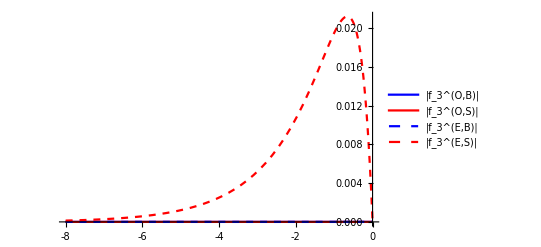

```mathematica
f3OB=0;
f3OS=(ⅈ η ((b12+b21) ⅇ^(-ⅈ qe (x+x1)) γe γh-(a41+a32) ⅇ^(ⅈ qh (x+x1)) γe γh-(a21+a12) ⅇ^(ⅈ (qh x-qe x1)) γh^2 √((1-γe^2)/(1-γh^2))+(b41+b32) ⅇ^(-ⅈ qe x+ⅈ qh x1) γe^2 √((1-γh^2)/(1-γe^2))))/(8(qh γe-qe γh))-1/(8(qh γe-qe γh))ⅈ(-(b41+b32) ⅇ^(ⅈ (qh x-qe x1)) γe^2 √((-1+γh^2)/(-1+γe^2))+γh ((a21+a12) ⅇ^(-ⅈ qe x+ⅈ qh x1) √((-1+γe^2)/(-1+γh^2)) γh+(-(b12+b21) ⅇ^(-ⅈ qe (x+x1))+(a41+a32) ⅇ^(ⅈ qh (x+x1))) γe)) η;
f3EB=0;
f3ES=(ⅈ η ((b12+b21) ⅇ^(-ⅈ qe (x+x1)) γe γh-(a41+a32) ⅇ^(ⅈ qh (x+x1)) γe γh-(a21+a12) ⅇ^(ⅈ (qh x-qe x1)) γh^2 √((1-γe^2)/(1-γh^2))+(b41+b32) ⅇ^(-ⅈ qe x+ⅈ qh x1) γe^2 √((1-γh^2)/(1-γe^2))))/(8(qh γe-qe γh))+1/(8(qh γe-qe γh))ⅈ(-(b41+b32) ⅇ^(ⅈ (qh x-qe x1)) γe^2 √((-1+γh^2)/(-1+γe^2))+γh ((a21+a12) ⅇ^(-ⅈ qe x+ⅈ qh x1) √((-1+γe^2)/(-1+γh^2)) γh+(-(b12+b21) ⅇ^(-ⅈ qe (x+x1))+(a41+a32) ⅇ^(ⅈ qh (x+x1))) γe)) η;
(*fuuES=(ⅈ η ((a22+a11) * (ⅇ^(-ⅈ qe x+ⅈ qh x1)-ⅇ^(ⅈ (qh x-qe x1)))*γh^2 √((1-γe^2)/(1-γh^2))+(a22+a11) (ⅇ^(-ⅈ qe x+ⅈ qh x1)-ⅇ^(ⅈ (qh x-qe x1))) γe^2 √((1-γh^2)/(1-γe^2))))/(8(qh γe-qe γh));*)
Plot[{Abs[f3OB],Abs[f3OS],Abs[f3EB],Abs[f3ES]},{x,0,-8ξ},(*AxesLabel->{"x/ξ",None},*)AxesLabel->(MaTeX[#,Magnification->20/12]&)/@{"x/\\xi"},AxesOrigin->{0,0},PlotRange->{{0,-8ξ},{-0.0001,All}},TicksStyle->Directive[Black],BaseStyle->{FontFamily->"Times",FontSize->13},Ticks->{{{0,"0"},{- 2ξ,"-2"},{- 4ξ,"-4"},{- 6ξ,"-6"},{-8ξ,"-8"}},Automatic},AxesStyle->{Thickness[0.002],Thickness[0.002]},LabelStyle->Directive[Black],PlotStyle->{{Blue},{Red},{Blue,Dashed},{Red,Dashed}},PlotRange->All,PlotLegends->Placed[{{Style["|\!\(\*SuperscriptBox[SubscriptBox[\(f\), \(  3  \)], \(O,B\)]\)|",FontFamily->"Times"],Style["|\!\(\*SuperscriptBox[SubscriptBox[\(f\), \(  3  \)], \(O,S\)]\)|",FontFamily->"Times"],Style["|\!\(\*SuperscriptBox[SubscriptBox[\(f\), \( 3 \)], \(E,B\)]\)|",FontFamily->"Times"],Style["|\!\(\*SuperscriptBox[SubscriptBox[\(f\), \( 3 \)], \(E,S\)]\)|",FontFamily->"Times"]}},{Left,Top}]]
```